```mathematica
Practical 1
Aim:Bisection Method
```

```mathematica
Example 1 
The function f (x)=1.15-1.04*x+Log[x] has a zero on the interval (1,3).Perform five iterations and use the bisection method to approximate the root.
```

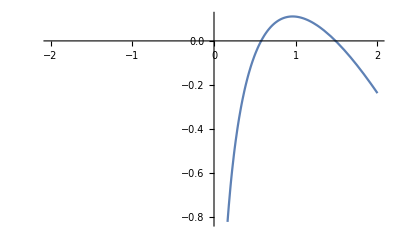

{{y[x]→5 x+x^2+C[1]}}

```mathematica
bisection[f_,ao_,bo_,n_]:=Module[{},a=N[ao];
b=N[bo];
If[f[a]*f[b]>0,Print["Bisection method can not applied"];
Return[]];
p=(a+b)/2;
i=1;
While[i≤n,If[f[a]*f[b]<0,b=p,a=p];
Print[i,"  ",a,"  ",b];
i++;
p=(a+b)/2];
Print["Roots=",p]];
f[x_]:=1.15-1.04*x+Log[x];
Plot[f[x],{x,-2,2}]
eqn=DSolve[y'[x]==2*x+5,y[x],x]
```

```mathematica
bisection[f,1,3,5]
```

1  1.  2.

2  1.  1.5

3  1.  1.25

4  1.125  1.25

5  1.1875  1.25

Roots=1.21875

```mathematica
Example 2
The function f (x)=x^3+x^2-3*x-3  has a zero on the interval (0,2).Perform five iterations and use the bisection method to approximate the root.
```

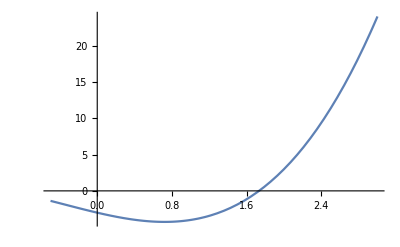

```mathematica
f[x_]:=x^3+x^2-3*x-3;
Plot[f[x],{x,-0.5,3}]
```

```mathematica
bisection[f,0,2,5]
```

1  0.  1.

2  0.5  1.

3  0.75  1.

4  0.875  1.

5  0.9375  1.

Roots=0.96875

```mathematica
Example 3
The function f (x)= Sin[x]+E^x  has a zero on the interval (-1,1).Perform five iterations and use the bisection method to approximate the root.
```

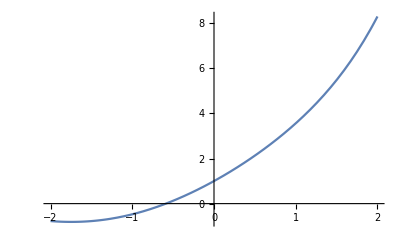

```mathematica
f[x_]:=Sin[x]+E^x;
Plot[f[x],{x,-2,2}]
```

```mathematica
bisection[f,-1,1,5]
```

1  -1.  0.

2  -1.  -0.5

3  -1.  -0.75

4  -0.875  -0.75

5  -0.8125  -0.75

Roots=-0.78125